```mathematica
SetDirectory[NotebookDirectory[]];
```

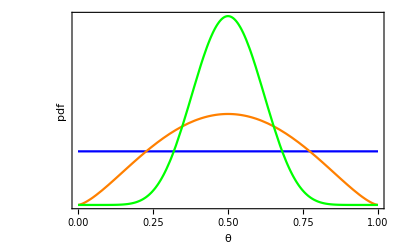

```mathematica
g1=Plot[{PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[2.5,2.5],x],PDF[BetaDistribution[10,10],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},BaseStyle->Medium,FrameTicks->{True,None},PlotStyle->{Blue,Orange,Green}]
```

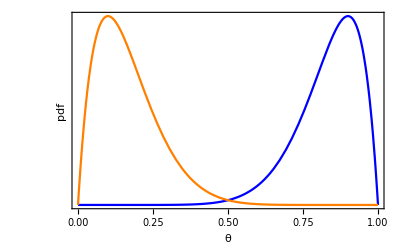

```mathematica
g2=Plot[{PDF[BetaDistribution[10,2],x],PDF[BetaDistribution[2,10],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},BaseStyle->Medium,FrameTicks->{True,None},PlotStyle->{Blue,Orange}]
```

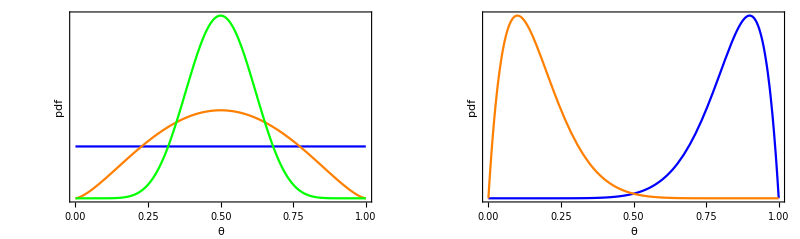

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_betaDistribution.pdf",gFinal]
```

Distributions_betaDistribution.pdf